# Skeleton-based Analysis of Melt Network

## Functions

```mathematica
Clear["Global`*"];
```

readSkel[path] reads .ply skeleton file as a table and returns points, lines and radius:

```mathematica
readSkel:= Function[path, 
	rawData = Import[path,"Table"];
	numOfPoints = rawData⟦3,3⟧;
	numOfEdges = rawData⟦9,3⟧;
	dataTable = rawData⟦15;;,;;⟧;
	
	burnTime = dataTable⟦;;numOfPoints,1⟧;
	Points = dataTable⟦;;numOfPoints,3;;5⟧;
	Lines = dataTable⟦numOfPoints+1;;⟧ + 1;
	Radius = dataTable⟦;;numOfPoints,2⟧;
	{Points,Lines,Radius,burnTime}
]
```

```mathematica
readSkel2:= Function[path, 
	rawData = Import[path,"Table"];
	numOfPoints = rawData⟦3,3⟧;
	numOfEdges = rawData⟦9,3⟧;
	dataTable = rawData⟦15;;,;;⟧;
	
	burnTime = dataTable⟦;;numOfPoints,1⟧;
	Points = dataTable⟦;;numOfPoints,3;;5⟧;
	Lines = dataTable⟦numOfPoints+1;;⟧ + 1;
	Radius = dataTable⟦;;numOfPoints,2⟧;
	{Points,Lines,Radius,burnTime}
]
```

getRange[list] returns the range(min and max value) of elements in the list:

```mathematica
getRange:=Function[list,
	min = Min[list];
	max = Max[list];
	{min, max}]
```

move[from, to] add an offset to list from based on the distance between center of range2 and range1:

```mathematica
move:=Function[{from,to},
	range1 = getRange[from];
	range2 = getRange[to];
	offset = (range2⟦1⟧ + range2⟦2⟧-range1⟦1⟧ - range1⟦2⟧)/2;
	res = from + offset;
	res]
```

coordsAlign[coords1, coords2] add offsets to each dimension of coords1 so that coords1 is aligned with coords2. coords1, coords2: N by 3(x,y,z)

```mathematica
coordsAlign:=Function[{coords1,coords2},
	newX = move[coords1⟦;;,1⟧,coords2⟦;;,1⟧];
	newY = move[coords1⟦;;,2⟧,coords2⟦;;,2⟧];
	newZ = move[coords1⟦;;,3⟧,coords2⟦;;,3⟧];
	newCoords1 = {newX,newY,newZ};
	Transpose[newCoords1]]
```

linesToGraph[lines] construct a graph based on the lines

```mathematica
linesToGraph:=Function[{lines},
	graph=Graph[Table[lines⟦i,1⟧<->lines⟦i,2⟧,{i,1,Dimensions[lines]⟦1⟧}]]
]
```

getJunctions[graph] collect all junction nodes(degree >= 3) and their degree from a graph

```mathematica
getJunctions:=Function[{graph},
	ans={};
	For[i=1,i≤VertexCount[graph],i++,
	degree = VertexDegree[graph,i];
	If[degree>2,AppendTo[ans,{i,degree}]]];
	ans
]
```

InitJG[points, lines, radius] generates a list of junctions and a simplified graph based on these junctions
	Inputs: 
		points: a list of all points in skeleton
		lines: a list of all lines in skeleton
		radius: a list of radius of each point in skeleton
	Returns:
		junctionDataTable: a list of all basic junctions {identifier, degree, cluster, coordinate, radius}
		simplifiedG: a simplified graph which eliminates all vertices with degree of 2

```mathematica
initJG:= Function[{points, lines, radius,burntime},
	skelGraph = linesToGraph[lines];
	Print["Initial graph built!"];
	simplifiedG = simplifyGraph[skelGraph];
	Print["simplified graph done!"];
	junctions = getJunctions[skelGraph];
	junctionsDataTable = Table[{junctions⟦i,1⟧,junctions⟦i,2⟧,{{junctions⟦i,1⟧,points⟦junctions⟦i,1⟧,;;⟧,radius⟦junctions⟦i,1⟧⟧}},points⟦junctions⟦i,1⟧,;;⟧,radius⟦junctions⟦i,1⟧⟧,burntime⟦junctions⟦i,1⟧⟧},{i,Dimensions[junctions]⟦1⟧}];	
	(*junctionsDataTable = Select[junctionsDataTable,#⟦6⟧ > 1 &];*)
	Print["Basic junctions computed!"];
	{junctionsDataTable, simplifiedG}
]
```

```mathematica
computeAngle:=Function[{vec1,vec2},
	If[Norm[vec1]*Norm[vec2] == 0, 
		angle = 0,
		cosValue=vec1.vec2/(Norm[vec1]*Norm[vec2]);
		angle = ArcCos[cosValue]/(2*Pi) * 360;
	];
	angle
]
```

```mathematica
computeStdAngle:=Function[d,
	points = SpherePoints[d];
	minAngle = 180;
	For[i=1, i≤Length[points] - 1,i++,
		For[j =i+1, j≤ Length[points], j++,
			theAngle = computeAngle[points⟦i⟧-{0,0,0},points⟦j⟧-{0,0,0}];
			minAngle = Min[theAngle, minAngle]; 
		]
	];
	minAngle
]
```

```mathematica
angleScore:=Function[{allPoints,c,d,stdAngle},
	edges=c⟦7⟧;
	aScore = -100;
	n=Length[edges];
	For[i=1,i≤n-1,i++,
		edge1=edges⟦i⟧;
		point11=allPoints⟦edge1⟦1⟧,;;⟧;
		point12=allPoints⟦edge1⟦2⟧,;;⟧;
		vec1=point12-point11;
		For[j=i+1,j≤n,j++,
			edge2=edges⟦j⟧;
			point21=allPoints⟦edge2⟦1⟧,;;⟧;
			point22=allPoints⟦edge2⟦2⟧,;;⟧;
			vec2=point22-point21;
			theAngle=computeAngle[vec1,vec2];
			aScore = Max[aScore, Abs[theAngle - stdAngle] / 15];
		];
	];
	aScore
]
```

```mathematica
clusterAngleScore:= Function[{simplifiedG,allPoints, c1, c2, d},
	stdAngle = computeStdAngle[d];
	aScore1 = angleScore[allPoints, c1, d, stdAngle];
	aScore2 = angleScore[allPoints, c2, d, stdAngle];
	worstScore = Max[aScore1, aScore2];
	worstScore
]
```

distanceScore[ball1, ball2] computes the score which tell whether the two balls should be merged
	ball1: {identifier, {x1,y1,z1}, r1} 
	ball2: {identifier, {x2,y2,z2}, r2}

```mathematica
distanceScore := Function[{ball1, ball2},
	r1 = Max[ball1⟦3⟧,ball2⟦3⟧];
	r2 = Min[ball1⟦3⟧,ball2⟦3⟧];
	d = EuclideanDistance[ball1⟦2⟧, ball2⟦2⟧];
	(*score = If[r2==0, If[r1==0,d, (-r1+d)/r1],(-r1 - r2 + d)/r2];*)
	score = If[r2==0, -r1+d,(-r1 - r2 + d)/(2*r2)];
	score
]
```

clusterDistanceScore[simplifiedG,c1,c2] computes the distance score between cluster c1 and cluster c2
Inputs:
	c1, c2: a merged junction {identifier, degree, cluster, coordinate, radius}
Return:
	worstScore: the worst distance score among all scores between each ball in  c1 and each ball in c2

```mathematica
clusterDistanceScore:= Function[{initSimplifiedG,c1,c2},
	worstScore = -100;
	ballList1 = c1⟦3⟧;
	ballList2 = c2⟦3⟧;
	For[i=1, i≤Length[ballList1],i++,
		For[j=1, j≤Length[ballList2],j++,
			(*If[EdgeQ[initSimplifiedG,ballList1⟦i,1⟧<->ballList2⟦j,1⟧],*)
				worstScore = Max[worstScore, distanceScore[ballList1⟦i⟧, ballList2⟦j⟧]];
			(*]*)
		]
	];
	worstScore
]
```

clusterMergeScore[c1,c2] computes the worst score between cluster c1 and cluster c2
Inputs:
	c1, c2: a merged junction {identifier, degree, cluster, coordinate, radius}
Return:
	worstScore: the minimum score among all scores between each ball in  c1 and each ball in c2

```mathematica
clusterMergeScore:= Function[{simplifiedG,,initSimpleG,allPoints,c1,c2},
	dScore = clusterDistanceScore[initSimpleG, c1, c2];
	innerDegree = Length[EdgeList[simplifiedG,c1⟦1⟧<->c2⟦1⟧]];
	(*d = c1⟦2⟧ + c2⟦2⟧ - innerDegree * 2;*)
	d = VertexDegree[simplifiedG, c1⟦1⟧] + VertexDegree[simplifiedG, c2⟦1⟧] - innerDegree * 2;
	aScore = clusterAngleScore[simplifiedG,allPoints,c1,c2,d];
	totalScore=(d-1)/d*dScore + 1/d*aScore;
	{dScore, aScore, totalScore}
]
```

```mathematica
isMergable:=Function[{dScore},
	If[dScore ≤ 1, 
		True, 
		False
	]
]
```

```mathematica
deleteNode := Function[{graph, v},
	resGraph = graph;
	If[VertexDegree[graph, v] ≠ 2, Throw[resGraph]];
	
	neighbors = AdjacencyList[resGraph,v];
	v1 = neighbors⟦1⟧;
	v2 = If[Length[neighbors] == 2,neighbors⟦2⟧, neighbors⟦1⟧];
	
	resGraph = VertexDelete[resGraph, v];
	resGraph = EdgeAdd[resGraph,v1<->v2];
	resGraph
]
```

```mathematica
simplifyGraph := Function[{skelGraph},
	g = skelGraph;
	nodesDeg2 = Pick[VertexList[g], VertexDegree[g], 2];
	
	While[Length[nodesDeg2] > 0,
		g = Catch[deleteNode[g, nodesDeg2⟦1⟧]];
		nodesDeg2 = Drop[nodesDeg2,1];
		If[Mod[Length[nodesDeg2],500]==0,Print[Length[nodesDeg2]]];
	];
	g
]
```

smallestCircumBall[ball1,ball2] computes the smallest circumscribe ball of ball1 and ball2
Inputs:
	ball: {identifier, degree, cluster, coordinate, radius}
Return:
	{c,r}: c is the center and r is the radius

```mathematica
smallestCircumBall:=Function[{ball1,ball2},
	c1 = ball1⟦4⟧;
	r1 = ball1⟦5⟧;
	c2 = ball2⟦4⟧;
	r2 = ball2⟦5⟧;
	
	d = EuclideanDistance[c1, c2];
	
	If[d == 0, Throw[{c1,Max[r1,r2]}]];
	
	t1 = r1/d;
	t2 = -r1/d;
	t3 = 1+r2/d;
	t4 = 1-r2/d;
	tmax = Max[t1,t2,t3,t4];
	tmin = Min[t1,t2,t3,t4];
	c3 = c1 + (tmax+tmin)/2*(c2-c1);
	r3 = (Abs[tmax]+Abs[tmin])/2*d;
	{c3,r3}
]
```

mergeJunctions[ball1,ball2] merges ball1 and ball2
inputs:
	junctionList: {identifier, degree, cluster, coordinate, radius}
		cluster is a list of nodes {identifier,{x,y,z},radius}
	graph: the simplified graph showing connectivity relationship of junctions
	ball: {identifier, degree, cluster, coordinate, radius}
return: 
	a list consisting of an updated junction list and an updated graph

```mathematica
mergeJunctions:= Function[{junctionList, graph, ball1, ball2},
	newJunctionList = junctionList;

	v1 = ball1⟦1⟧;
	v2 = ball2⟦1⟧;
	innerEdges = EdgeList[graph,v1<->v2];
	
	g = EdgeDelete[graph, innerEdges];
	g = VertexReplace[g,{v2->v1}];
	
	newDegree = VertexDegree[g,v1];
	
	{c3,r3}= Catch[smallestCircumBall[ball1,ball2]];
	newClusterList=Join[ball1⟦3⟧,ball2⟦3⟧];
	
	newBall = {v1,newDegree,newClusterList,c3,r3,{}};
	
	newJunctionList = DeleteCases[newJunctionList,ball1];
	newJunctionList = DeleteCases[newJunctionList,ball2];
	newJunctionList = AppendTo[newJunctionList,newBall];

	{newJunctionList, g, newBall}
]
```

```mathematica
updateEdgeListByID:=Function[{edgeList, oldID, newID},
	newEdgeList = edgeList;
	For[i=1, i≤Length[edgeList], i++,
		edge=edgeList⟦i⟧;
		If[edge⟦1⟧==oldID, edge⟦1⟧=newID];
		If[edge⟦2⟧==oldID, edge⟦2⟧=newID];
		newEdgeList⟦i⟧=edge;
	];
	newEdgeList
]
```

```mathematica
recomputeCandidateEdgeScore:=Function[{initSimplifiedG,junctionList,candidateEdgeList,j},
	newCandidateEdgeList = candidateEdgeList;
	For[i=1,i<=Length[candidateEdgeList],i++,
		edge=candidateEdgeList⟦i,1⟧;
		If[edge⟦1⟧==j || edge⟦2⟧==j,
			ball1 = Select[junctionList,#⟦1⟧ == edge⟦1⟧ &]⟦1⟧;
			ball2 = Select[junctionList,#⟦1⟧ == edge⟦2⟧ &]⟦1⟧;
			newCandidateEdgeList⟦i,2⟧=clusterDistanceScore[initSimplifiedG,ball1,ball2];
			Print["i:",i," Length:",Length[candidateEdgeList]];
		];
	];
	Sort[newCandidateEdgeList, #1⟦2⟧ < #2⟦2⟧ &]
]
```

computeCN[junctionList, graph] merges the junctions and return the junction list and graph after merging
Inputs:
	junctionList: {identifier, degree, cluster, coordinate, radius}
		cluster is a list of nodes {identifier,{x,y,z},radius}
	graph: the simplified graph before merging
Returns:
	J: merged junctions
	G: the graph after merging

```mathematica
computeCN:=Function[{junctionList,initSimpleG,allPoints},
	J = junctionList;
	G = initSimpleG;
	candidateEdgeList = {};
	(*While[True,*)
		tgt1 = {};
		tgt2 = {};
		
		edges = EdgeList[G];
		Do[
			j1 = edge⟦1⟧;
			j2 = edge⟦2⟧;
			
			If[j1 == j2, Continue[]];
			
			c1 = Select[J,#⟦1⟧ == j1 &];
			c2 = Select[J,#⟦1⟧ == j2 &];

			If[c1 == {} || c2 == {}, Continue[]];
			
			c1 = c1⟦1⟧;
			c2 = c2⟦1⟧;
	
			dScore=clusterDistanceScore[initSimpleG,c1,c2];
			
			If[isMergable[dScore] && !MemberQ[candidateEdgeList⟦;;,1⟧, j1<->j2] && !MemberQ[candidateEdgeList⟦;;,1⟧, j2<->j1],
				AppendTo[candidateEdgeList, {edge, dScore}];
			];
		,{edge,edges}];
		
		If[Length[candidateEdgeList] == 0, Break[]];
		candidateEdgeList = Sort[candidateEdgeList, #1⟦2⟧ < #2⟦2⟧ &];
	
		While[Length[candidateEdgeList]>0,
			Print[Length[candidateEdgeList]];
			
			candidateEdge = candidateEdgeList⟦1,1⟧;
			tgt1 = candidateEdge⟦1⟧;
			tgt2 = candidateEdge⟦2⟧;
			ball1 = Select[J,#⟦1⟧ == tgt1 &]⟦1⟧;
			ball2 = Select[J,#⟦1⟧ == tgt2 &]⟦1⟧;
			{J,G} = mergeJunctions[J,G,ball1,ball2];

			candidateEdgeList=Drop[candidateEdgeList,1];
			candidateEdgeList⟦;;,1⟧=updateEdgeListByID[candidateEdgeList⟦;;,1⟧,ball2⟦1⟧,ball1⟦1⟧];
			candidateEdgeList = Select[candidateEdgeList, #⟦1,1⟧!=#⟦1,2⟧ &];
			candidateEdgeList=recomputeCandidateEdgeScore[initSimpleG,J,candidateEdgeList,tgt1];
			Print["new:",Length[candidateEdgeList]];
		];
	(*];*)
	{J,G}
]
```

```mathematica
computeCN2:=Function[{junctionList,initSimpleG,allPoints},
	J = junctionList;
	G = initSimpleG;
	JunctionHistory = {};
	threshHold = 1;
	
	While[True,
		tgt1 = {};
		tgt2 = {};
		bestScore = threshHold+100;
		edges = EdgeList[G];
		Do[
			j1 = edge⟦1⟧;
			j2 = edge⟦2⟧;
			
			If[j1 == j2, Continue[]];
			
			c1 = Select[J,#⟦1⟧ == j1 &];
			c2 = Select[J,#⟦1⟧ == j2 &];

			If[c1 == {} || c2 == {}, Continue[]];
			
			c1 = c1⟦1⟧;
			c2 = c2⟦1⟧;
	
			dScore=clusterDistanceScore[initSimpleG,c1,c2];
			If[dScore<bestScore,
				tgt1=c1;
				tgt2=c2;
				bestScore=dScore;
			]
			
		,{edge,edges}];
		
		If[bestScore>threshHold,
			Break[];
		];
		
		Print[bestScore];
		
		snapshot = {J,{tgt1,tgt2}};
		
		{J,G,mergedBall} = mergeJunctions[J,G,tgt1,tgt2];
		
		AppendTo[snapshot⟦2⟧,mergedBall];
		AppendTo[JunctionHistory,snapshot];
	];
	{J,G,JunctionHistory}
]
```

```mathematica
degreeColor:=Function[d,
	Switch[d,
		2, Black,
		3, Brown,
		4, Yellow,
		5, Magenta,
		6, Cyan,
		7, Red,
		_, Blue
	]
]
```

## Function Test

### test data

test getRange[list], move[from, to]

```mathematica
list1 = {1,2.5,3.7,4}; list2 = {5,6,7,8};
list1 = move[list1,list2]
```

{5,6.5,7.7,8}

test coordsAlign[coords1, coords2]

```mathematica
coords1={{0,0,0},{0,1,0},{0,0,1},{0,1,1},{1,0,0},{1,1,0},{1,0,1},{1,1,1}};
coords2={{2,1,4},{2,2,4},{2,1,5},{2,2,5},{3,1,4},{3,2,4},{3,1,5},{3,2,5}};
coords3=coordsAlign[coords1,coords2]

a = Graphics3D[{
	Red,Point[coords1],
	Green,Point[coords2],
	Red,Opacity[0.3],Ball[coords3,0.1]
}];
Show[a]
```

{{2,1,4},{2,2,4},{2,1,5},{2,2,5},{3,1,4},{3,2,4},{3,1,5},{3,2,5}}

-Graphics3D-

test linesToGraph[lines] and getJunctions[graph]

```mathematica
testLines = {{1,2},{2,3},{1,4},{4,3},{1,3},{3,1}};
(*testLines = {{1,2},{1,2}};*)
g = linesToGraph[testLines]
```

-Graphics-

test deleteNode[graph, v], simplifyGraph[graph]

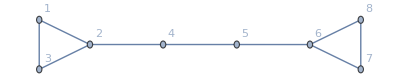

```mathematica
g = Graph[{1<-> 2, 2 <-> 3, 3 <-> 1,2<->4,4<->5,5<->6,6<->7,7<->8,8<->6}, VertexLabels -> "Name"]
(*s = simplifyGraph[g];
GraphPlot3D[s]*)
```

```mathematica
EdgeQ[g,5<->4]
```

True

test mergeScore

```mathematica
ball1 = {{1,2,3},2};
ball2 = {{4,5,6},6};
mergeScore[ball1, ball2]
```

mergeScore[{{1,2,3},2},{{4,5,6},6}]

test simplifyGraph

```mathematica
g = Graph[{1<-> 2, 2 <-> 3, 3 <-> 1,2<->4,4<->5,5<->6,6<->7,7<->8,8<->6}, VertexLabels -> "Name"]
h = simplifyGraph[g];
GraphPlot3D[h]
```

-Graphics-

0

-Graphics3D-

test smallestCircumBall

```mathematica
c1 = {0,0,0};
r1 = 1;
c2 = {0.1,0.5,0.6};
r2 = 0.4;
{c3,r3} = smallestCircumBall[{1,2,c1,r1},{1,2,c2,r2}]

a1 = Ball[c1,r1];
a2 = Ball[c2,r2];
a3 = Ball[c3,r3];

Graphics3D[{
	Opacity[0.5],
	Green,a1,
	Blue,a2,
	Red,a3}]
```

Part::partw: Part 5 of {1,2,{0,0,0},1} does not exist.

Part::partw: Part 5 of {1,2,{0.1,0.5,0.6},0.4} does not exist.

{1-0.3 (Max[-1.66667 {1,2,{0,0,0},1}⟦5⟧,1.66667 {1,2,{0,0,0},1}⟦5⟧,1-1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧,1+1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧]+Min[-1.66667 {1,2,{0,0,0},1}⟦5⟧,1.66667 {1,2,{0,0,0},1}⟦5⟧,1-1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧,1+1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧]),0.3 (Abs[Max[-1.66667 {1,2,{0,0,0},1}⟦5⟧,1.66667 {1,2,{0,0,0},1}⟦5⟧,1-1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧,1+1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧]]+Abs[Min[-1.66667 {1,2,{0,0,0},1}⟦5⟧,1.66667 {1,2,{0,0,0},1}⟦5⟧,1-1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧,1+1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧]])}

-Graphics3D-

```mathematica
a=Graph[{1<->2,1<->2,1<->3,4<->2}]
```

-Graphics-

```mathematica
b=EdgeList[a,1<->_]
```

{1<->2,1<->2,1<->3}

```mathematica
c=EdgeList[a,2<->_]
```

{1<->2,1<->2,4<->2}

```mathematica
d=Join[b,c]
```

{1<->2,1<->2,1<->3,1<->2,1<->2,4<->2}

```mathematica
e={1,2};
```

```mathematica
Select[d, (MemberQ[e, #⟦1⟧]&&!MemberQ[e, #⟦2⟧])||(!MemberQ[e, #⟦1⟧]&&MemberQ[e, #⟦2⟧]) &]
```

{1<->3,4<->2}

## Code

### Set working directory

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Excel Data

```mathematica
groundTruthTable = Import["data\\scoba12.xlsx"];
```

Import::nffil: File data\scoba12.xlsx not found during Import.

```mathematica
groundTruthTable = groundTruthTable[[1,;;,;;]];
trueJunctions = groundTruthTable[[;;,{4,5,6,10,19}]];
```

Part::partd: Part specification $Failed⟦1,1;;All,1;;All⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1,1;;All,1;;All⟧⟦1;;All,{4,5,6,10,19}⟧ is longer than depth of object.

### scoba12_small

#### Medial Axis

```mathematica
maRawData = Import["scoba12_small.ply","Table"];
maTable = maRawData⟦15;;,;;⟧;
maPoints = maTable⟦;;86117,;;⟧;
maPoints = coordsAlign[maPoints,skelPoints];
maPolygons = maTable⟦363203;;,10;;12⟧ + 1;
```

Import::nffil: File scoba12_small.ply not found during Import.

Part::take: Cannot take positions 15 through -1 in $Failed.

Part::take: Cannot take positions 1 through 86117 in $Failed⟦15;;All,1;;All⟧.

Part::partd: Part specification $Failed⟦1,1⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 86117 of 15;;All does not exist.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 3 of 1;;86117 does not exist.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::take: Cannot take positions 363203 through -1 in $Failed⟦15;;All,1;;All⟧.

```mathematica
polygonInCoords = Table[{Blue,Polygon[{maPoints⟦maPolygon⟦1⟧⟧,maPoints⟦maPolygon⟦2⟧⟧,maPoints⟦maPolygon⟦3⟧⟧}]},{maPolygon,maPolygons}];
```

Table::iterb: Iterator {maPolygon,1+$Failed⟦15;;All,1;;All⟧⟦363203;;All,10;;12⟧} does not have appropriate bounds.

#### Skeleton & Junctions

```mathematica
{thepoints,thelines,theradius,burnTime}=readSkel["scoba12_small_skel.ply"];
```

```mathematica
theSelectedLines = Select[thelines, (burnTime⟦#⟦1⟧⟧+burnTime⟦#⟦2⟧⟧)/2 > 1 &];
```

```mathematica
{theJ,theG}=initJG[thepoints,theSelectedLines,theradius,burnTime];
```

Initial graph built!

11000

10500

10000

9500

9000

8500

8000

7500

7000

6500

6000

5500

5000

4500

4000

3500

3000

2500

2000

1500

1000

500

0

simplified graph done!

Basic junctions computed!

```mathematica
{theJres,theGres,theJuncHistory}=computeCN2[theJ,theG,thepoints];
```

-1.

-0.923012

-0.885953

-0.882231

-0.84327

-0.841034

-0.837167

-0.826851

-0.818951

-0.815507

-0.81114

-0.795902

-0.79543

-0.787718

-0.780084

-0.779928

-0.77511

-0.774675

-0.769483

-0.737247

-0.728107

-0.727862

-0.720568

-0.717151

-0.714177

-0.706582

-0.705235

-0.693967

-0.6904

-0.674201

-0.652421

-0.630399

-0.617448

-0.595613

-0.59175

-0.577681

-0.57735

-0.577188

-0.577159

-0.576012

-0.569737

-0.56966

-0.56966

-0.56966

«1 more identical outputs»

-0.569651

-0.569505

-0.566461

-0.565717

-0.56451

-0.559842

-0.550802

-0.539801

-0.531212

-0.523374

-0.512273

-0.497231

-0.49244

-0.486729

-0.476446

-0.448457

-0.438388

-0.435015

-0.422743

-0.422649

-0.422649

-0.422649

«1 more identical outputs»

-0.399853

-0.388838

-0.367418

-0.361779

-0.331942

-0.26145

-0.250082

-0.223721

-0.221793

-0.216702

-0.184693

-0.183503

-0.183503

-0.155198

-0.144709

-0.139508

-0.139345

-0.119923

-0.0777584

-0.0316758

-0.00389932

4.6625×10^-7

0.0792502

0.138564

0.140756

0.160506

0.166603

0.180956

0.180956

0.194413

0.206864

0.23215

0.243552

0.288351

0.28863

0.290579

0.29758

0.297626

0.3539

0.363619

0.382713

0.383921

0.414214

0.414214

0.521441

0.614904

0.623691

0.627949

0.656436

0.675

0.688754

0.774183

0.825743

0.827401

0.88111

0.896058

0.91138

0.914855

0.914855

0.963764

```mathematica
Length[theJ]
Length[theJres]
Dimensions[theJuncHistory]
```

294

166

{128,2}

## Cubes

### Cube1

```mathematica
{points1,lines1,radius1} = readSkel["data\\cube1\\cube1_skel.ply"];
```

Import::nffil: File data\cube1\cube1_skel.ply not found during Import.

Part::partd: Part specification $Failed⟦3,3⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦9,3⟧ is longer than depth of object.

Part::take: Cannot take positions 15 through -1 in $Failed.

Part::span: 1;;$Failed⟦3,3⟧ is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::span: 1+$Failed⟦3,3⟧;;All is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stop: Further output of Part::span will be suppressed during this calculation.

Set::shape: Lists {points1,lines1,radius1} and {$Failed⟦15;;All,1;;All⟧⟦1;;$Failed⟦3,3⟧,3;;5⟧,1+$Failed⟦15;;All,1;;All⟧⟦1+$Failed⟦3,3⟧;;All⟧,$Failed⟦15;;All,1;;All⟧⟦1;;$Failed⟦3,3⟧,2⟧,$Failed⟦15;;All,1;;All⟧⟦1;;$Failed⟦3,3⟧,1⟧} are not the same shape.

```mathematica
{J1,G1}=initJG[points1,lines1,radius1];
```

Function::fpct: Too many parameters in {points,lines,radius,burntime} to be filled from Function[{points,lines,radius,burntime},skelGraph=linesToGraph[lines];Print[Initial graph built!];simplifiedG=simplifyGraph[skelGraph];«1»;«1»;«1»;junctionsDataTable=Select[«18»,«1»>1&];Print[Basic junctions computed!];{junctionsDataTable,simplifiedG}][«1»].

Set::shape: Lists {J1,G1} and Function[{points,lines,radius,burntime},skelGraph=linesToGraph[lines];Print[Initial graph built!];simplifiedG=simplifyGraph[skelGraph];«1»;«1»;«1»;junctionsDataTable=Select[«18»,«1»>1&];Print[Basic junctions computed!];{junctionsDataTable,simplifiedG}][«1»] are not the same shape.

```mathematica
Export["data\\cube1\\basicJunctions1.xls", J1, "XLS"];
adjMatrix1 = AdjacencyMatrix[G1];
Export["data\\cube1\\adjMatrix1.tgf", adjMatrix1];
```

Export::type: AdjacencyMatrix cannot be exported to the TGF format.

```mathematica
{Jres1,Gres1}=computeCN[J1,G1];
```

Function::fpct: Too many parameters in {junctionList,initSimpleG,allPoints} to be filled from Function[{junctionList,initSimpleG,allPoints},«1»][J1,G1].

Set::shape: Lists {Jres1,Gres1} and Function[{junctionList,initSimpleG,allPoints},«1»][J1,G1] are not the same shape.

```mathematica
Export["data\\cube1\\mergedJunctions1.xls", Jres1, "XLS"];
adjMatrixRes1 = AdjacencyMatrix[Gres1];
Export["data\\cube1\\adjMatrixRes1.tgf", adjMatrixRes1];
```

Export::type: AdjacencyMatrix cannot be exported to the TGF format.

```mathematica
CNs = Jres1⟦;;,2⟧;
Histogram[CNs]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Histogram::ldata: Symbol[] is not a valid dataset or list of datasets.

Histogram[Symbol[]]

### Cube2

```mathematica
{points2,lines2,radius2} = readSkel["data\\cube2\\cube2_skel.ply"];
```

Import::nffil: File data\cube2\cube2_skel.ply not found during Import.

Part::partd: Part specification $Failed⟦3,3⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦9,3⟧ is longer than depth of object.

Part::take: Cannot take positions 15 through -1 in $Failed.

Part::span: 1;;$Failed⟦3,3⟧ is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::span: 1+$Failed⟦3,3⟧;;All is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stop: Further output of Part::span will be suppressed during this calculation.

Set::shape: Lists {points2,lines2,radius2} and {$Failed⟦15;;All,1;;All⟧⟦1;;$Failed⟦3,3⟧,3;;5⟧,1+$Failed⟦15;;All,1;;All⟧⟦1+$Failed⟦3,3⟧;;All⟧,$Failed⟦15;;All,1;;All⟧⟦1;;$Failed⟦3,3⟧,2⟧,$Failed⟦15;;All,1;;All⟧⟦1;;$Failed⟦3,3⟧,1⟧} are not the same shape.

```mathematica
{J2,G2}=initJG[points2,lines2,radius2];
```

Function::fpct: Too many parameters in {points,lines,radius,burntime} to be filled from Function[{points,lines,radius,burntime},skelGraph=linesToGraph[lines];Print[Initial graph built!];simplifiedG=simplifyGraph[skelGraph];«1»;«1»;«1»;junctionsDataTable=Select[«18»,«1»>1&];Print[Basic junctions computed!];{junctionsDataTable,simplifiedG}][«1»].

Set::shape: Lists {J2,G2} and Function[{points,lines,radius,burntime},skelGraph=linesToGraph[lines];Print[Initial graph built!];simplifiedG=simplifyGraph[skelGraph];«1»;«1»;«1»;junctionsDataTable=Select[«18»,«1»>1&];Print[Basic junctions computed!];{junctionsDataTable,simplifiedG}][«1»] are not the same shape.

```mathematica
Export["data\\cube2\\basicJunctions2.xls", J2, "XLS"];
adjMatrix2 = AdjacencyMatrix[G2];
Export["data\\cube2\\adjMatrix2.tgf",adjMatrix2];
```

Export::type: AdjacencyMatrix cannot be exported to the TGF format.

```mathematica
G22 = Import["data\\cube2\\adjMatrix2.tgf"];
J22 = Import["data\\cube2\\basicJunctions2.xls"];
```

Import::nffil: File data\cube2\adjMatrix2.tgf not found during Import.

```mathematica
{Jres2,Gres2}=computeCN[J2,G2];
```

Function::fpct: Too many parameters in {junctionList,initSimpleG,allPoints} to be filled from Function[{junctionList,initSimpleG,allPoints},«1»][J2,G2].

Set::shape: Lists {Jres2,Gres2} and Function[{junctionList,initSimpleG,allPoints},«1»][J2,G2] are not the same shape.

```mathematica
Export["data\\cube2\\mergedJunctions2.xls", Jres2, "XLS"];
adjMatrixRes2 = AdjacencyMatrix[Gres2];
Export["data\\cube2\\adjMatrixRes2.tgf",adjMatrixRes2];
```

Export::type: AdjacencyMatrix cannot be exported to the TGF format.

```mathematica
CNs2 = Jres2⟦;;,2⟧;
Histogram[CNs2]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Histogram::ldata: Symbol[] is not a valid dataset or list of datasets.

Histogram[Symbol[]]

#### Visualization

```mathematica
J2=Import["data\\cube2\\basicJunctions2.xls"]⟦1⟧;
J2=ToExpression[J2];
J2⟦;;,4⟧=coordsAlign[J2⟦;;,4⟧,points2];
```

Part::partw: Part 4 of {{{J2}}} does not exist.

Part::partd: Part specification {{{{J2}}}}⟦1;;All,4⟧⟦1;;All,1⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 2 of {{{{J2}}}} does not exist.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 3 of {{{{J2}}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Set::partw: Part 4 of {{{J2}}} does not exist.

```mathematica
cube2BasicBalls=Table[{Ball[J2⟦i,4⟧,J2⟦i,5⟧]},{i,Dimensions[J2]⟦1⟧}];
```

Part::partw: Part 4 of {{{J2}}} does not exist.

Part::partw: Part 5 of {{{J2}}} does not exist.

```mathematica
Jres2=Import["data\\cube2\\mergedJunctions2.xls"]⟦1⟧;
Jres2=ToExpression[Jres2];
Jres2⟦;;,4⟧=coordsAlign[Jres2⟦;;,4⟧,points2];
```

Part::partw: Part 4 of {{{Jres2}}} does not exist.

Part::partd: Part specification {{{{Jres2}}}}⟦1;;All,4⟧⟦1;;All,1⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 2 of {{{{Jres2}}}} does not exist.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 3 of {{{{Jres2}}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Set::partw: Part 4 of {{{Jres2}}} does not exist.

```mathematica
cube2JunctionBalls=Table[{Ball[Jres2⟦i,4⟧,Jres2⟦i,5⟧]},{i,Dimensions[Jres2]⟦1⟧}];
```

Part::partw: Part 4 of {{{Jres2}}} does not exist.

Part::partw: Part 5 of {{{Jres2}}} does not exist.

```mathematica
Show[Graphics3D[{skelCube2,{Opacity[0.5],Blue,cube2JunctionBalls},{Opacity[0.5],Red,cube2BasicBalls}}]]
```

-Graphics3D-

### Cube3

```mathematica
{points3,lines3,radius3} = readSkel["data\\cube3\\cube3_skel.ply"];
```

Import::nffil: File data\cube3\cube3_skel.ply not found during Import.

Part::partd: Part specification $Failed⟦3,3⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦9,3⟧ is longer than depth of object.

Part::take: Cannot take positions 15 through -1 in $Failed.

Part::span: 1;;$Failed⟦3,3⟧ is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::span: 1+$Failed⟦3,3⟧;;All is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stop: Further output of Part::span will be suppressed during this calculation.

Set::shape: Lists {points3,lines3,radius3} and {$Failed⟦15;;All,1;;All⟧⟦1;;$Failed⟦3,3⟧,3;;5⟧,1+$Failed⟦15;;All,1;;All⟧⟦1+$Failed⟦3,3⟧;;All⟧,$Failed⟦15;;All,1;;All⟧⟦1;;$Failed⟦3,3⟧,2⟧,$Failed⟦15;;All,1;;All⟧⟦1;;$Failed⟦3,3⟧,1⟧} are not the same shape.

```mathematica
{J3,G3}=initJG[points3,lines3,radius3];
```

Function::fpct: Too many parameters in {points,lines,radius,burntime} to be filled from Function[{points,lines,radius,burntime},skelGraph=linesToGraph[lines];Print[Initial graph built!];simplifiedG=simplifyGraph[skelGraph];«1»;«1»;«1»;junctionsDataTable=Select[«18»,«1»>1&];Print[Basic junctions computed!];{junctionsDataTable,simplifiedG}][«1»].

Set::shape: Lists {J3,G3} and Function[{points,lines,radius,burntime},skelGraph=linesToGraph[lines];Print[Initial graph built!];simplifiedG=simplifyGraph[skelGraph];«1»;«1»;«1»;junctionsDataTable=Select[«18»,«1»>1&];Print[Basic junctions computed!];{junctionsDataTable,simplifiedG}][«1»] are not the same shape.

```mathematica
Export["data\\cube3\\basicJunctions3.xls", J3, "XLS"];
adjMatrix3 = AdjacencyMatrix[G3];
```

```mathematica
Export["data\\cube3\\adjMatrix3.tgf",adjMatrix3];
```

Export::type: AdjacencyMatrix cannot be exported to the TGF format.

```mathematica
{Jres3,Gres3}=computeCN[J3,G3];
```

Function::fpct: Too many parameters in {junctionList,initSimpleG,allPoints} to be filled from Function[{junctionList,initSimpleG,allPoints},«1»][J3,G3].

Set::shape: Lists {Jres3,Gres3} and Function[{junctionList,initSimpleG,allPoints},«1»][J3,G3] are not the same shape.

```mathematica
Export["data\\cube3\\mergedJunctions3.xls", Jres3, "XLS"];
adjMatrixRes3 = AdjacencyMatrix[Gres3];
```

```mathematica
Export["data\\cube3\\adjMatrixRes3.tgf",adjMatrixRes3];
```

Export::type: AdjacencyMatrix cannot be exported to the TGF format.

```mathematica
CNs = Jres3⟦;;,2⟧
Histogram[CNs]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Symbol[]

Histogram::ldata: Symbol[] is not a valid dataset or list of datasets.

Histogram[Symbol[]]

#### Visualization

```mathematica
J3=Import["data\\cube3\\basicJunctions3.xls"]⟦1⟧;
J3=ToExpression[J3];
J3⟦;;,4⟧=coordsAlign[J3⟦;;,4⟧,points3];
```

Part::partw: Part 4 of {{{J3}}} does not exist.

Part::partd: Part specification {{{{J3}}}}⟦1;;All,4⟧⟦1;;All,1⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 2 of {{{{J3}}}} does not exist.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 3 of {{{{J3}}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Set::partw: Part 4 of {{{J3}}} does not exist.

```mathematica
cube3BasicBalls=Table[{Ball[J3⟦i,4⟧,J3⟦i,5⟧]},{i,Dimensions[J3]⟦1⟧}];
```

Part::partw: Part 4 of {{{J3}}} does not exist.

Part::partw: Part 5 of {{{J3}}} does not exist.

```mathematica
Jres3=Import["data\\cube3\\mergedJunctions3.xls"]⟦1⟧;
Jres3=ToExpression[Jres3];
Jres3⟦;;,4⟧=coordsAlign[Jres3⟦;;,4⟧,points3];
```

Part::partw: Part 4 of {{{Jres3}}} does not exist.

Part::partd: Part specification {{{{Jres3}}}}⟦1;;All,4⟧⟦1;;All,1⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 2 of {{{{Jres3}}}} does not exist.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 3 of {{{{Jres3}}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Set::partw: Part 4 of {{{Jres3}}} does not exist.

```mathematica
cube3JunctionBalls=Table[{Ball[Jres3⟦i,4⟧,Jres3⟦i,5⟧]},{i,Dimensions[Jres3]⟦1⟧}];
```

Part::partw: Part 4 of {{{Jres3}}} does not exist.

Part::partw: Part 5 of {{{Jres3}}} does not exist.

```mathematica
Show[Graphics3D[{skelCube3,{Opacity[0.5],Blue,cube3JunctionBalls},{Opacity[0.5],Red,cube3BasicBalls}}]]
```

-Graphics3D-

### Cube4

```mathematica
{points4,lines4,radius4} = readSkel["data\\cube4\\cube4_skel.ply"];
```

Import::nffil: File data\cube4\cube4_skel.ply not found during Import.

Part::partd: Part specification $Failed⟦3,3⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦9,3⟧ is longer than depth of object.

Part::take: Cannot take positions 15 through -1 in $Failed.

Part::span: 1;;$Failed⟦3,3⟧ is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::span: 1+$Failed⟦3,3⟧;;All is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stop: Further output of Part::span will be suppressed during this calculation.

Set::shape: Lists {points4,lines4,radius4} and {$Failed⟦15;;All,1;;All⟧⟦1;;$Failed⟦3,3⟧,3;;5⟧,1+$Failed⟦15;;All,1;;All⟧⟦1+$Failed⟦3,3⟧;;All⟧,$Failed⟦15;;All,1;;All⟧⟦1;;$Failed⟦3,3⟧,2⟧,$Failed⟦15;;All,1;;All⟧⟦1;;$Failed⟦3,3⟧,1⟧} are not the same shape.

```mathematica
{J4,G4}=initJG[points4,lines4,radius4];
```

Function::fpct: Too many parameters in {points,lines,radius,burntime} to be filled from Function[{points,lines,radius,burntime},skelGraph=linesToGraph[lines];Print[Initial graph built!];simplifiedG=simplifyGraph[skelGraph];«1»;«1»;«1»;junctionsDataTable=Select[«18»,«1»>1&];Print[Basic junctions computed!];{junctionsDataTable,simplifiedG}][«1»].

Set::shape: Lists {J4,G4} and Function[{points,lines,radius,burntime},skelGraph=linesToGraph[lines];Print[Initial graph built!];simplifiedG=simplifyGraph[skelGraph];«1»;«1»;«1»;junctionsDataTable=Select[«18»,«1»>1&];Print[Basic junctions computed!];{junctionsDataTable,simplifiedG}][«1»] are not the same shape.

```mathematica
Export["basicJunctions4.xls", J4, "XLS"];
adjMatrix4 = AdjacencyMatrix[G4];
Export["adjMatrix4.xls",adjMatrix4,"XLS"];
```

```mathematica
{Jres4,Gres4}=computeCN[J4,G4];
```

Function::fpct: Too many parameters in {junctionList,initSimpleG,allPoints} to be filled from Function[{junctionList,initSimpleG,allPoints},«1»][J4,G4].

Set::shape: Lists {Jres4,Gres4} and Function[{junctionList,initSimpleG,allPoints},«1»][J4,G4] are not the same shape.

```mathematica
Export["mergedJunctions4.xls", Jres4, "XLS"];
adjMatrixRes4 = AdjacencyMatrix[Gres4];
Export["adjMatrixRes4.xls",adjMatrixRes4,"XLS"];
```

```mathematica
CNs = Jres1⟦;;,2⟧;
Histogram[CNs]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Histogram::ldata: Symbol[] is not a valid dataset or list of datasets.

Histogram[Symbol[]]

#### Visualization

```mathematica
Jres4=Import[]
```

Import::argt: Import called with 0 arguments; 1 or 2 arguments are expected.

Import[]

```mathematica
cube4JunctionBalls=
```

## Real-World Data Test & Visualization

### scoba12_Small

```mathematica
maGraphic = Import["scoba12_small.ply","Graphics3D"];
skelGraphic = Import["scoba12_small_skel.ply","Graphics3D"];
```

Import::nffil: File scoba12_small.ply not found during Import.

Import::nffil: File scoba12_small_skel.ply not found during Import.

```mathematica
Show[Graphics3D[{edgeInCoords}], maGraphic]
```

Show::gcomb: Could not combine the graphics objects in Show[,$Failed].

Show[-Graphics3D-,$Failed]

```mathematica
Show[skelGraphic, maGraphic]
```

Show::gcomb: Could not combine the graphics objects in Show[$Failed,$Failed].

Show[$Failed,$Failed]